```mathematica
(* First time MaTeX config, don't run *)
Needs["PacletManager`"]
ResourceFunction["MaTeXInstall"][](* Tex instalation and Ghostscript required*)
ConfigureMaTeX["pdfLaTeX" -> "C:\\Users\\Sergio\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe", "Ghostscript"->"C:\\Program Files\\gs\\gs10.04.0\\bin\\gswin64c.exe"]
```

PacletObject[…]

ConfigureMaTeX[pdfLaTeX→C:\Users\Sergio\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.04.0\bin\gswin64c.exe]

```mathematica
PacletObject[…]
```

PacletObject[…]

```mathematica
Needs["MaTeX`"] (* everytime load MaTeX for TeX and test it. !! run from here or the next cell*)
<<MaTeX`
MaTeX["x^2 + \\sin(x)"]
```

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

-Graphics-

```mathematica
(* values provided for the model *)
constPSI = -1.43 *(10^-3) (* KPa --> MPa *)
a = 8
b=5.39
c = 2+2.5*b
Ks = 20  (* using loomy sand for now and making cm/d --> microm/s *)
dr =6*(10^-4)  (* m root diameter *)
Zr=0.6  (* m rooting depth, should we use the 75% of it? *)
hc=20
RAIw=5 
RAI = 9.8 (*m^2/m^2 so dimentionless *)
gsrsat = 0.047  (* m / s MPa *)
LAI = 1.4
lsr= Sqrt[dr*Zr/RAIw] (* m --> microm *)
psillist ={0.0,0.1,0.2, 0.3, 0.4, 0.5, 0.6, 0.7} 
k1 = 0.005 (* m^2/W *)
k2 = 0.0016 (* 1/K^2 *)
Topt = 298 (* K *)
psil0 = -4.5 (* MPa *)
psil1 = -0.05 (* MPa *)
Dx =1250 (* g /kg -->kg/kg *)
RH=0.7  (* percentage as a number from 0 to 1 *)
R = 8.314 (* m^3 Pa / K mol *)
p0=101.325 * 10^3 (* MPa --> Pa*)
gamma = 9.81 (* kg /m^3 *)
gammaw = 9800 *(1/10^12) (* gammaw=g*rhow units  Kg/m^2 s^2 --> kg / microm^2 s^2 *)
rho =1.23 (* kg/m^3 *)
rhow = 998 (* kg/m^3 *)
vw = 18*(10^-3)/rhow (* m^3/mol *)
g =9.8 (* m^2/s *)
cp = 1012 (* Pa m^3 / kg K *)
ga =20 (* mm/s *)
gsmax =25 (* mm/s *)
gpmax =11.7 (* vulnerability curve microm/MPa s*)
cv=2
dv=2
phi0=400 (* W/m^2 *)
Ta0=20+273.15
```

-0.00143

8

5.39

15.475

20

3/5000

0.6

20

5

9.8

0.047

1.4

0.00848528

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7}

0.005

0.0016

298

-4.5

-0.05

1250

0.7

8.314

101325.

9.81

49/5000000000

1.23

998

9/499000

9.8

1012

20

25

11.7

2

2

400

293.15

```mathematica
(*  RAI[s_] =RAIw* s^a    we'll use the constant RAI from the table*)
```

```mathematica
Evap[gsrp_, psis_,psil_]= gsrp * (psis-psil)
```

gsrp (-psil+psis)

```mathematica
K[s_]= Ks*s^c
```

20 s^15.475

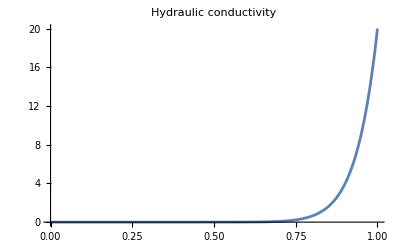

```mathematica
Plot[
K[s],{s,0,1},
PlotLabel->"Hydraulic conductivity",
PlotRange->{{0,1},{0,Ks}},
AxesLabel->{MaTeX["s"],MaTeX["K (cm/day)"]} ]
```

```mathematica
gsrp[gsr_, gp_]= (gsr*gp*LAI)/(gsr+LAI*gp) (*mm /s MPa*)
gsr[K_] = K/(g*rhow*lsr) *((10^10)/(60*60*24))(*mm/s MPa*)
gs[fphi_ ,fTa_, fpsil_,fD_]= gsmax*fphi*fTa*fpsil*fD  (*mm/s*)
gp[psil_]=gpmax*Exp[-((-psil/dv)^cv)] (*mm/s MPa*)
gsa[gs_,ga_]=(gs*ga)/(gs+ga)
(*use constant ga*)
```

(1.4 gp gsr)/(1.4 gp+gsr)

1394.64 K

25 fD fphi fpsil fTa

11.7 ⅇ^(-psil^2/4)

(20 gs)/(20+gs)

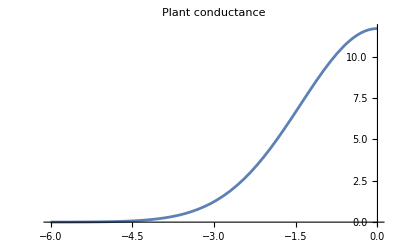

```mathematica
Plot[
gp[psil],{psil,-6,0},
PlotLabel->"Plant conductance",
AxesLabel->{MaTeX["\\psi_l"],MaTeX["g_p (\\mu m/MPa\cdot s)"]} ]
```

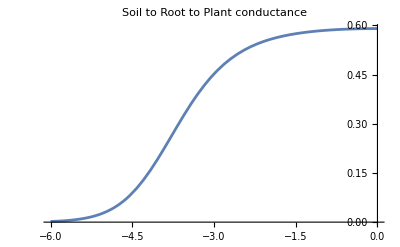

```mathematica
Plot[ 
gsrp[gsr[K[0.5]],gp[psil]],{psil,-6,0},
PlotLabel->"Soil to Root to Plant conductance",
AxesLabel->{MaTeX["\\psi_l"],MaTeX["g_{srp} (\\mu m/MPa\\cdot s)"]} ]
```

```mathematica
fphi[phi_]= 1-Exp[-k1*phi]
fTa[Ta_]=1-k2*(Ta-Topt)^2
fpsil[psil_]=Piecewise[{{(psil-psil0)/(psil1-psil0), psil0<=psil<=psil1},{0,psil<psil0}},1]
fD[D_]= 1 / (1 + (D/Dx))
```

1-ⅇ^(-0.005 phi)

1-0.0016 (-298+Ta)^2

Piecewise[{{0.224719 (4.5+psil), -4.5≤psil≤-0.05}, {0, psil<-4.5}, {1, True}}]

1/(1+D/1250)

```mathematica
esat[Ta_]=610.94*Exp[17.625*(Ta-273.15)/(Ta-273.15+243.04)] (* Pa *)
ea[Ta_] =RH*esat[Ta]
```

610.94 ⅇ^((17.625 (-273.15+Ta))/(-30.11+Ta))

427.658 ⅇ^((17.625 (-273.15+Ta))/(-30.11+Ta))

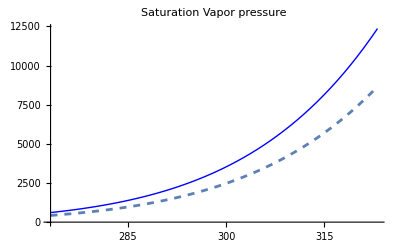

```mathematica
esatplot=Plot[
esat[Ta],{Ta,0+273.15,50+273.15},
PlotLabel->"Saturation Vapor pressure",
AxesLabel->{MaTeX["T (K)"],MaTeX["e_{sat} (Pa)"]},
PlotStyle->{Thick, Blue} ];
eaplot=Plot[
ea[Ta],{Ta,0+273.15,50+273.15},
AxesLabel->{MaTeX["T (K)"],MaTeX["e_{a} (Pa)"]} ,
PlotStyle->{Dashed}];
Show[esatplot, eaplot]
```

```mathematica
VPD[Ta_]= esat[Ta]-ea[Ta]
```

183.282 ⅇ^((17.625 (-273.15+Ta))/(-30.11+Ta))

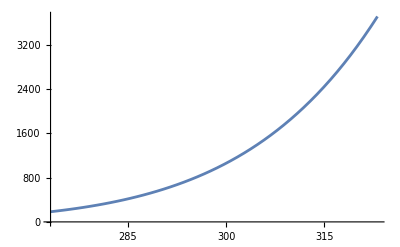

```mathematica
Plot[
VPD[Ta],{Ta,0+273.15,50+273.15},
AxesLabel->{MaTeX["T_a (K)"],MaTeX["VPD (Pa)"]} ]
```

```mathematica
el[Tl_,esat_,psil_]=esat*Exp[(vw*(psil-g*rhow*hc))/(R*Tl)]
```

ⅇ^((2.16936×10^-6 (-195608.+psil))/Tl) esat

```mathematica
(* Jarvis function plots *)
fphiplot=Plot[
fphi[phi],{phi,100,600},
PlotLabel->MaTeX["f_\\phi(\\phi)"],
AxesLabel->{MaTeX["\\phi"],MaTeX["f_\\phi"]} ];
fTaplot=Plot[
fTa[Ta], {Ta,273.15,313.15},
PlotLabel->MaTeX["f_{T_a}(T_a)"],
AxesLabel->{MaTeX["T_a"],MaTeX["f_{T_a}"]} ];
fDplot=Plot[
fD[D],{D,0,0.05},
PlotLabel->MaTeX["f_{D}(D)"],
AxesLabel->{MaTeX["D"],MaTeX["f_{D}"]} ];
fpsilplot=Plot[
fpsil[psil],{psil, -7,2},
PlotLabel->MaTeX["f_{\\psi_l}(\\psi_l)"],
AxesLabel->{MaTeX["\\psi_l"],MaTeX["f_{\\psi_l}"]} ];
```

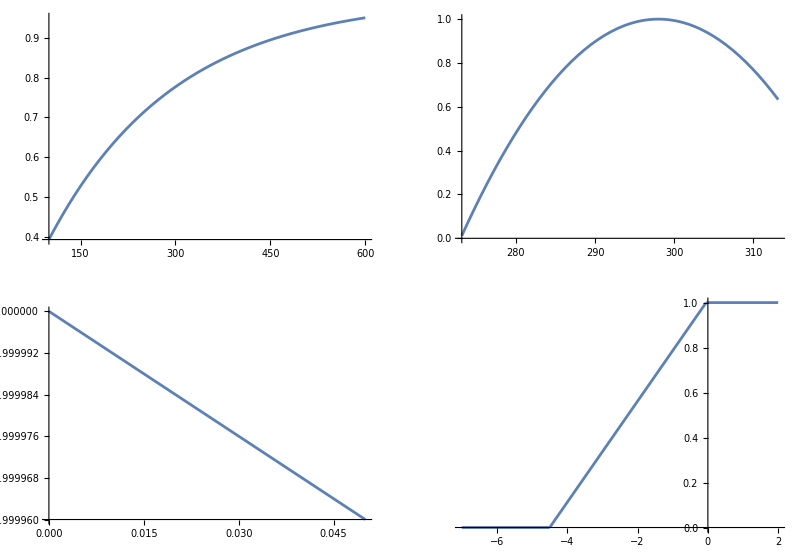

```mathematica
GraphicsGrid[{{fphiplot,fTaplot},{fDplot,fpsilplot}}]
```

8.1281

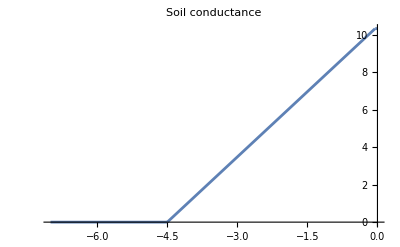

```mathematica
gs[fphi[phi0] ,fTa[303], fpsil[-1],fD[VPD[303]]]
Plot[
gs[fphi[phi0] ,fTa[303], fpsil[psil],fD[VPD[303]]],{psil,-7,0},
PlotLabel->"Soil conductance",
AxesLabel->{MaTeX["\\psi_l"],MaTeX["g_s (\\mu m/Mpa\\cdot s)"]} ]
```

```mathematica
psis[s_]= constPSI*s^(-b) 
psia[a_]= ((R*T/vw)Log[RH] + gammaw*Zr ) * (10^-6) (* Mpa conversion *)
```

-0.00143/s^5.39

(5.88×10^-9-164415. T)/1000000

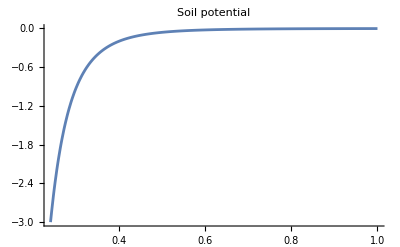

```mathematica
Plot[
psis[s],{s,0.2,1},
PlotLabel->"Soil potential",
PlotRange->{{0.2,1},{0,-3}},
AxesLabel->{MaTeX["s"],MaTeX["\\psi_s (MPa)"]} ]
```

```mathematica
Efinal[psil_,s_]=gsrp[gsr[K[s]], gp[psil]]*(psis[s]-psil)*(10^-3)*60*60*24
E2final[psil_,Tl_]= (rho/rhow)*gsa[gs[fphi[phi0] ,fTa[Ta0], fpsil[psil],fD[VPD[Ta0]]], ga]*(0.622/p0)*(el[Tl,esat[Tl],psil]- ea[Ta0])*60*60*24
```

(3.94749×10^7 ⅇ^(-psil^2/4) (-psil-0.00143/s^5.39) s^15.475)/(16.38 ⅇ^(-psil^2/4)+27892.9 s^15.475)

(0.174336 (-1633.41+610.94 ⅇ^((17.625 (-273.15+Tl))/(-30.11+Tl)+(2.16936×10^-6 (-195608.+psil))/Tl)) (Piecewise[{{0.224719 (4.5+psil), -4.5≤psil≤-0.05}, {0, psil<-4.5}, {1, True}}]))/(20+13.3351 (Piecewise[{{0.224719 (4.5+psil), -4.5≤psil≤-0.05}, {0, psil<-4.5}, {1, True}}]))

```mathematica
E35=Plot[Efinal[psil,0.35],{psil,-7,0}, PlotStyle->{Blue,Thick}];
E40=Plot[Efinal[psil,0.40],{psil,-7,0}, PlotStyle->{Blue,Thick}];
E293 = Plot[E2final[psil,293],{psil,-7,0}, PlotStyle->{Black}];
E298 = Plot[E2final[psil,298],{psil,-7,0}, PlotStyle->{Black}];
E303 = Plot[E2final[psil,303],{psil,-7,0}, PlotStyle->{Black}];
E308 = Plot[E2final[psil,308],{psil,-7,0}, PlotStyle->{Black}];
E313 = Plot[E2final[psil,313],{psil,-7,0}, PlotStyle->{Black}];
E318 = Plot[E2final[psil,318],{psil,-7,0}, PlotStyle->{Black}];
```

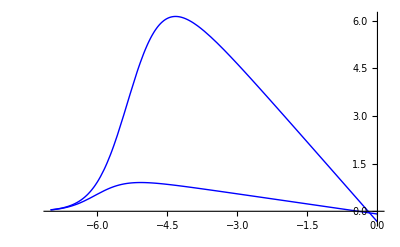

```mathematica
Show[E35,E40, PlotRange->All]
```

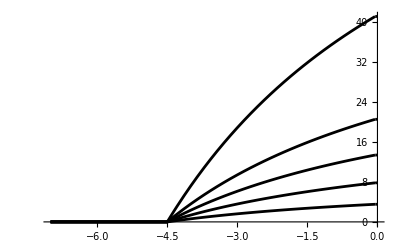

```mathematica
Show[E293,E298,E303,E308,E318, PlotRange-> All]
```

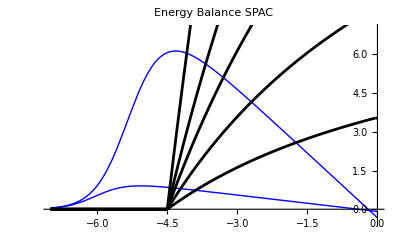

```mathematica
Show[E35,E40,E293,E298,E303,E308,E318, PlotRange-> {{-7,0},{-0.5,7}},
AxesLabel->{MaTeX["\\psi_l (MPa)"],MaTeX["E (mm/day)"]},PlotLabel->"Energy Balance SPAC"]
```

```mathematica
Export["C:\\Users\\Sergio\\Documents\\GitHub\\ecohydrology\\Assignments\\Ass5\\Energy balance 70.png",%137,"PNG"]
```

C:\Users\Sergio\Documents\GitHub\ecohydrology\Assignments\Ass5\Energy balance 70.png

```mathematica
(*Energy balance at the leaf*)(*find the solutions of the energy balance to interpolate later*)
solpsil=Table[FindRoot[Efinal[psil,0.40]-E2final[psil,Tl],{psil,-3}],{Tl,293,318,5}]
solpsil=psil/.solpsil
solEner=Efinal[solpsil,0.40]
solTemp=Table[Tl,{Tl,293,318,5}]
solfunction=Interpolation[Transpose@{solTemp,solEner}]
```

{{psil→-1.74397},{psil→-2.69915},{psil→-3.30053},{psil→-3.67874},{psil→-3.92242},{psil→-4.08366}}

{-1.74397,-2.69915,-3.30053,-3.67874,-3.92242,-4.08366}

{2.57946,4.15506,5.10053,5.62949,5.90659,6.04163}

{293,298,303,308,313,318}

InterpolatingFunction[…]

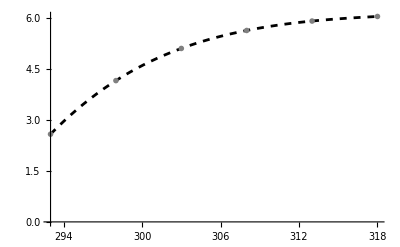

```mathematica
balance=Plot[solfunction[Tl],{Tl,293,318},PlotStyle->{Dashed,Black},AxesOrigin->{293,0}];
points=ListPlot[Transpose@{solTemp,solEner},PlotMarkers->"OpenMarkers",PlotStyle->{PointSize[Large],Gray}];
Show[balance,points]balance=Plot[solfunction[Tl],{Tl,293,318},PlotStyle->{Dashed,Black},AxesOrigin->{293,0}];
points=ListPlot[Transpose@{solTemp,solEner},PlotMarkers->"OpenMarkers",PlotStyle->{PointSize[Large],Gray}];
Show[balance,points]
```

```mathematica
(*Now we do the leaf energy balance*)
Q=400  (*W/m^2=kg m^2/s^3*)
rhow=998 (*kg/m^3*)
rho=1.23  (*kg/m^3*)
cp=1012  (*J/kg K=m^2/K s^2*)
ga=20/1000(*mm/s-->m/s*)
lambdaw[Ta_]=2.501*10^6-(2.361*10^(-3))*Ta;(*J/kg*)
E3final[Tl_]=(Q-rho*cp*ga*(Tl-Ta0))/(rhow*lambdaw[Ta0])*8.64*10^7
```

400

998

1.23

1012

1/50

0.0346154 (400-24.8952 (-293.15+Tl))

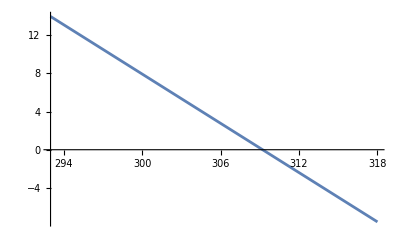

```mathematica
Eleaf=Plot[E3final[Tl],{Tl,293,318},AxesOrigin->{293,0}]
```

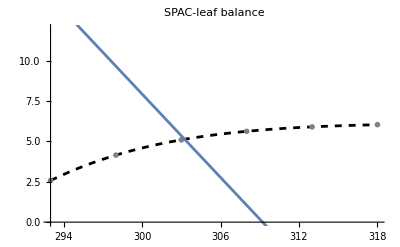

```mathematica
Show[balance,points,Eleaf,PlotRange->{{293,318},{0,12}},AxesLabel->{MaTeX["T_l (K)"],MaTeX["E (mm/day)"]},PlotLabel->"SPAC-leaf balance"]
```

```mathematica
Export["C:\\Users\\Sergio\\Documents\\GitHub\\ecohydrology\\Assignments\\Ass5\\Leaf-SPAC balance 70.png",%134,"PNG"]
```

C:\Users\Sergio\Documents\GitHub\ecohydrology\Assignments\Ass5\Leaf-SPAC balance 70.png

```mathematica
FindRoot[E3final[Tl]-solfunction[Tl],{Tl,300}]
E3final[303.257]
```

{Tl→303.257}

5.13638